Graphs
Original

```mathematica
ListPlot3D[Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\COVARIANCE\\cograph.dat", "Data"] , BaseStyle ->{FontSize -> 60}]
```

-Graphics3D-

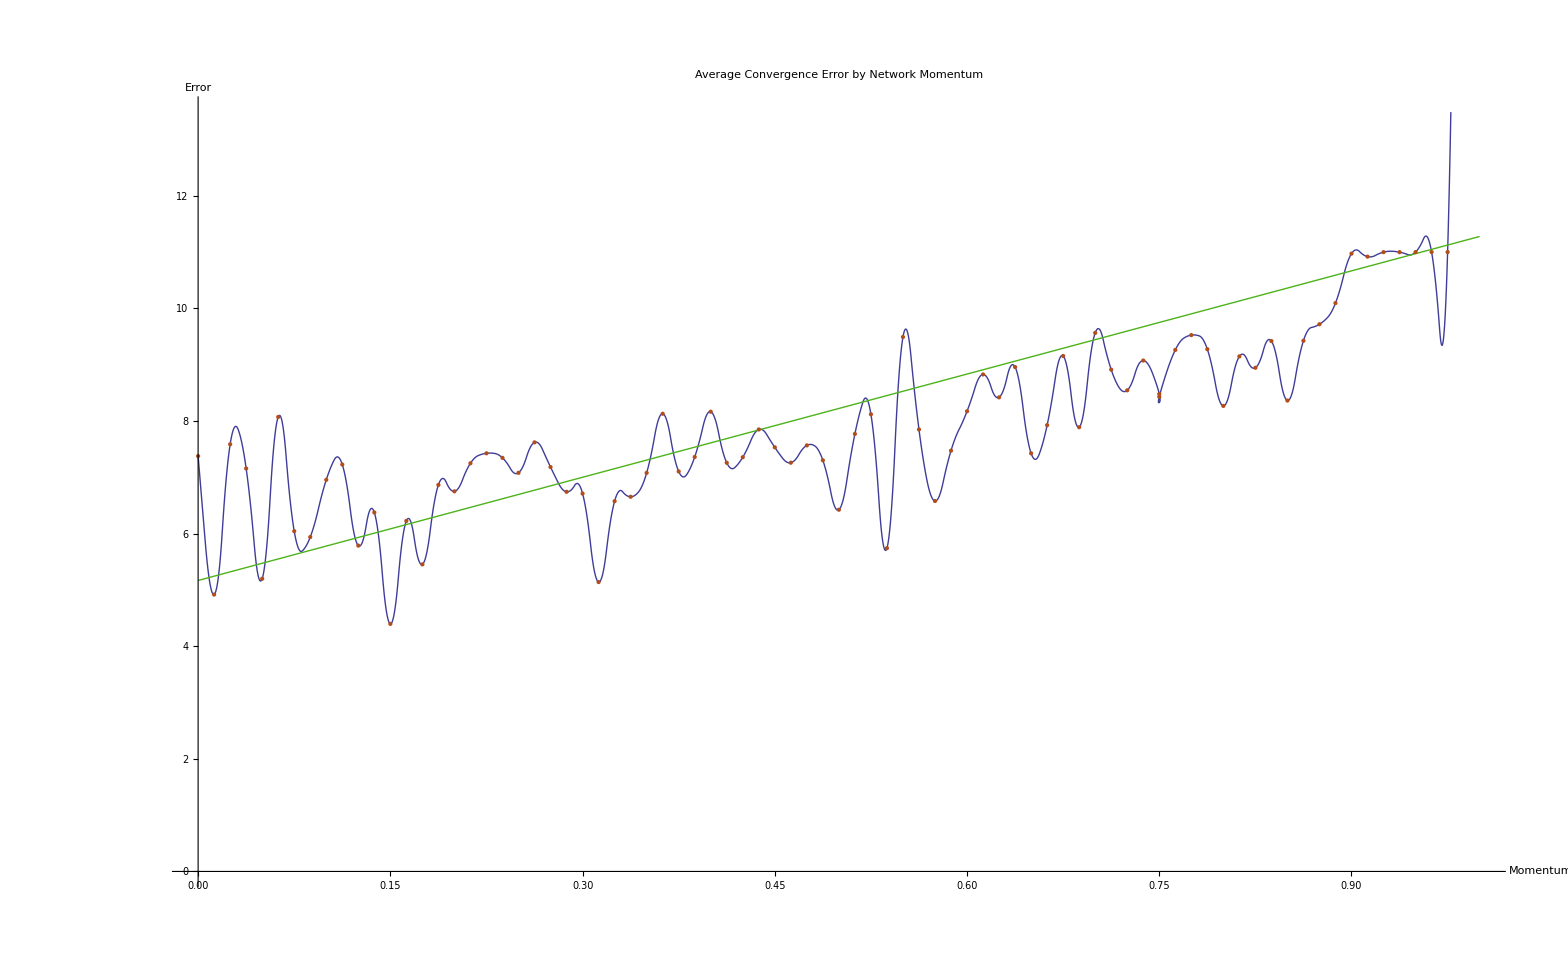

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\MM\\mmgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
Plot[Evaluate[Fit[data, {1,x}, x]],  {x,0,1},
 PlotStyle->{RGBColor[0.3,0.7,0.1]}],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["Momentum", FontSize->90],
Style["Error", FontSize->90]},
         PlotLabel->Style["Average Convergence Error by Network Momentum", FontSize->100], BaseStyle ->{FontSize -> 60}]
```

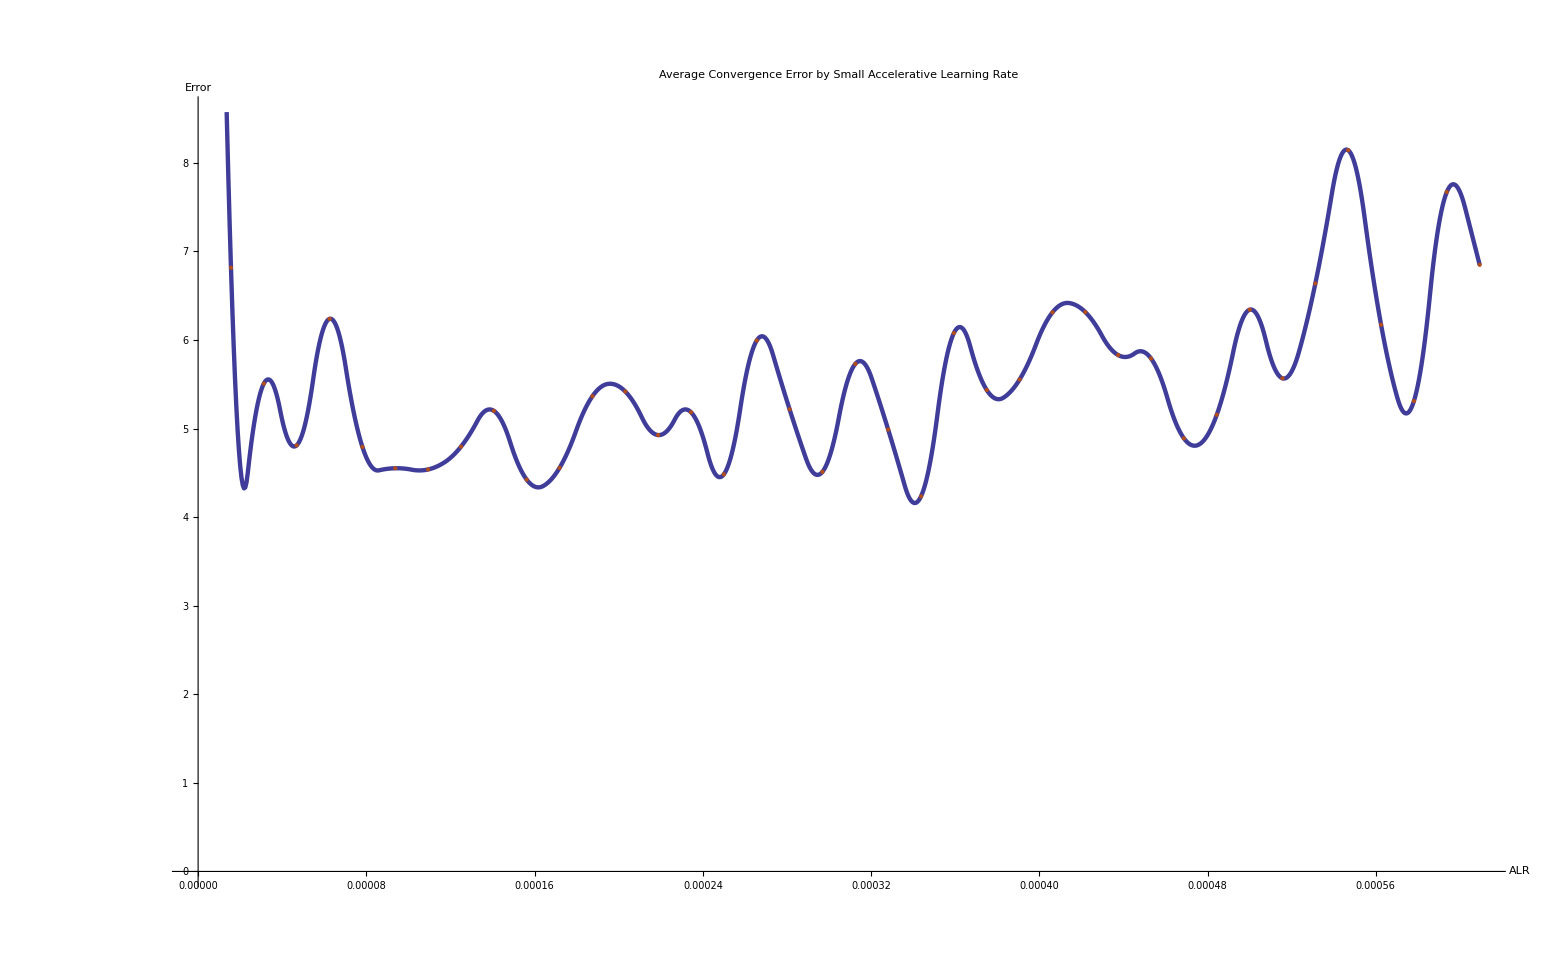

```mathematica
data2 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Smallest\\smallgraph.dat", "Data"];
Show[ListLinePlot[data2, PlotStyle->{Thickness[0.002]},InterpolationOrder->2],
ListPlot[data2, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->150],
Style["Error", FontSize->150]},
         PlotLabel->Style["Average Convergence Error by Small Accelerative Learning Rate", FontSize->220], BaseStyle ->{FontSize -> 120}]
```

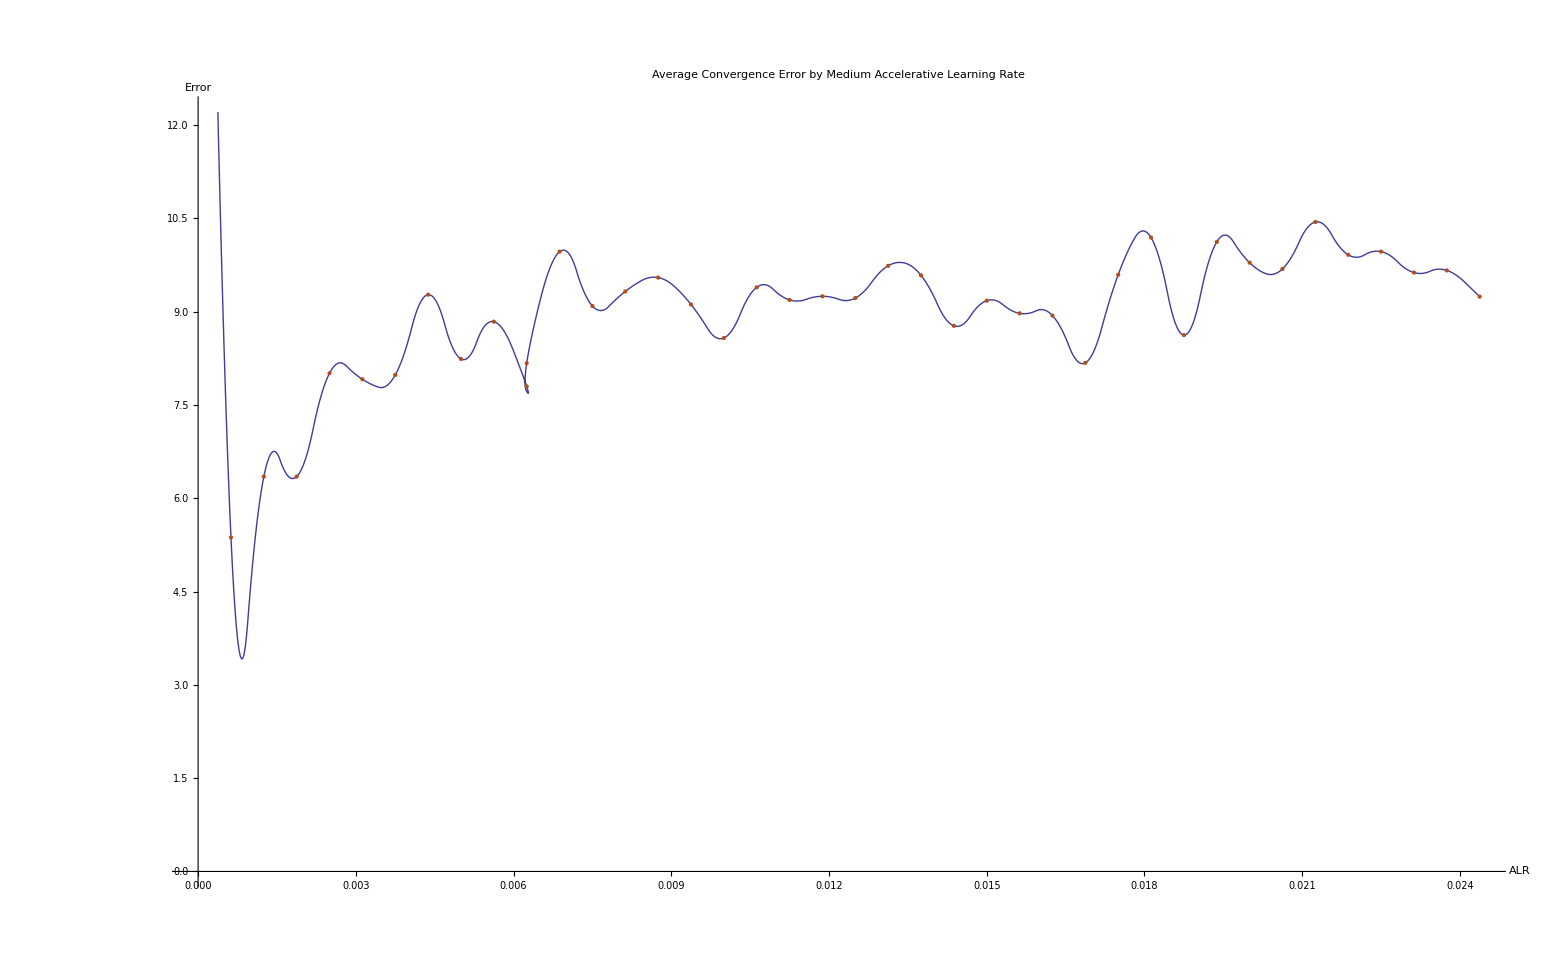

```mathematica
data3 = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Medium\\mediumgraph.dat", "Data"];
Show[ListLinePlot[data3, InterpolationOrder->2],
ListPlot[data3, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->120],
Style["Error", FontSize->120]},
         PlotLabel->Style["Average Convergence Error by Medium Accelerative Learning Rate", FontSize->100], BaseStyle ->{FontSize -> 60}]
```

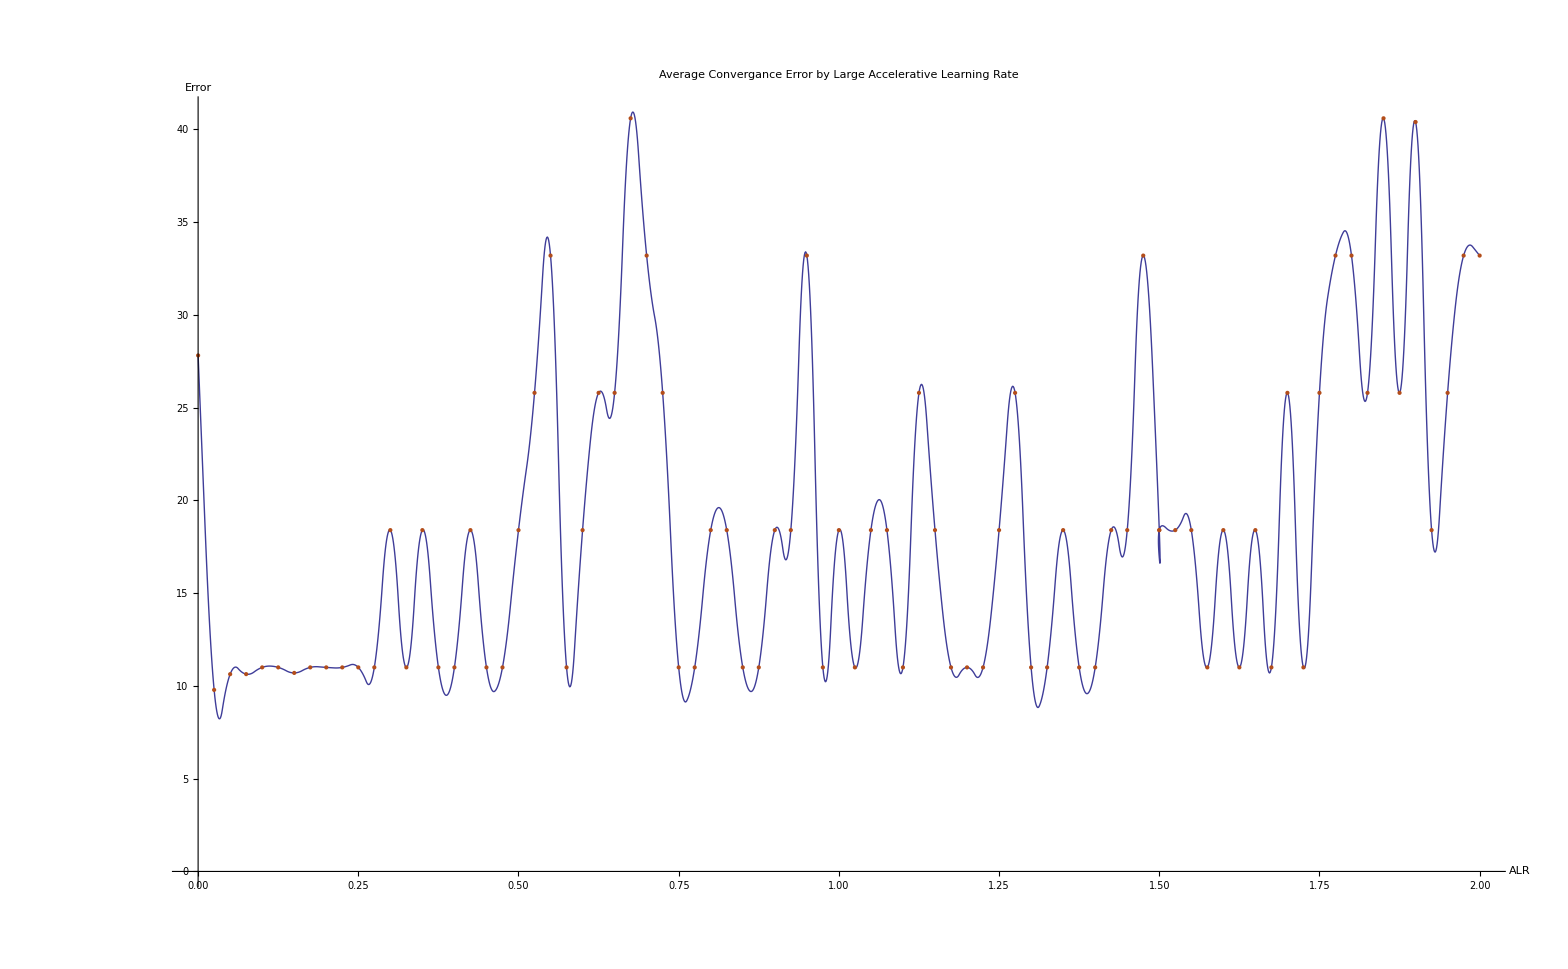

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\Large\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, InterpolationOrder->2],
ListPlot[data, PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->41],
Style["Error", FontSize->41]},
         PlotLabel->Style["Average Convergance Error by Large Accelerative Learning Rate", FontSize->76], BaseStyle ->{FontSize -> 30}]
```

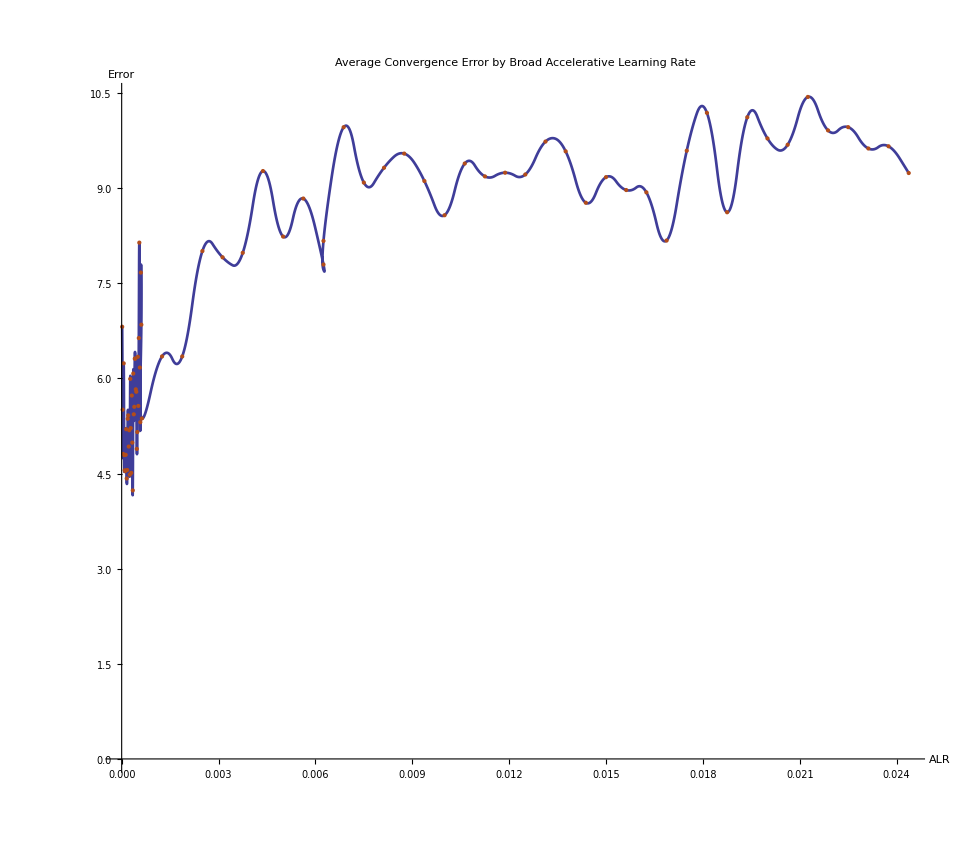

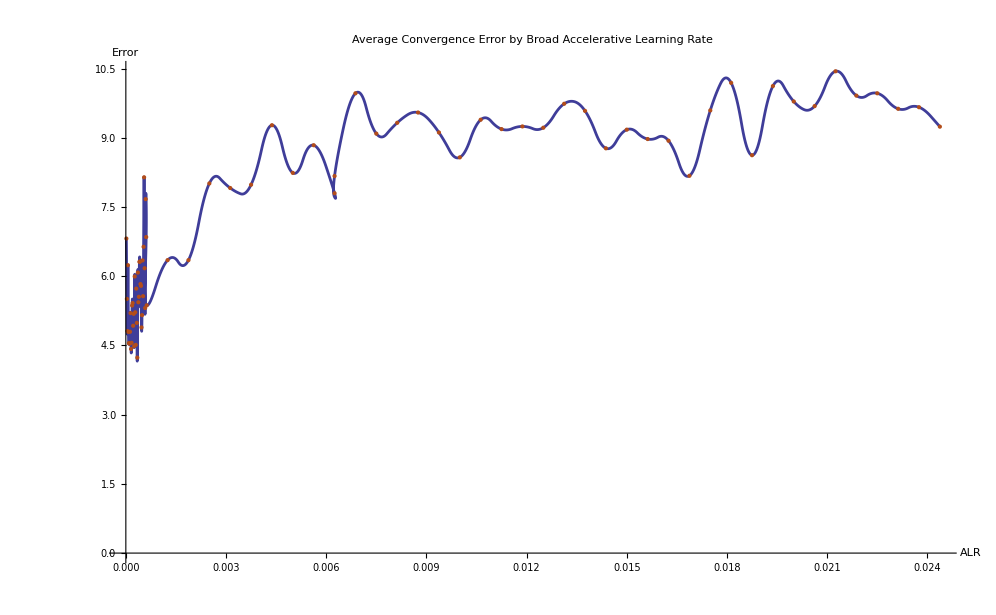

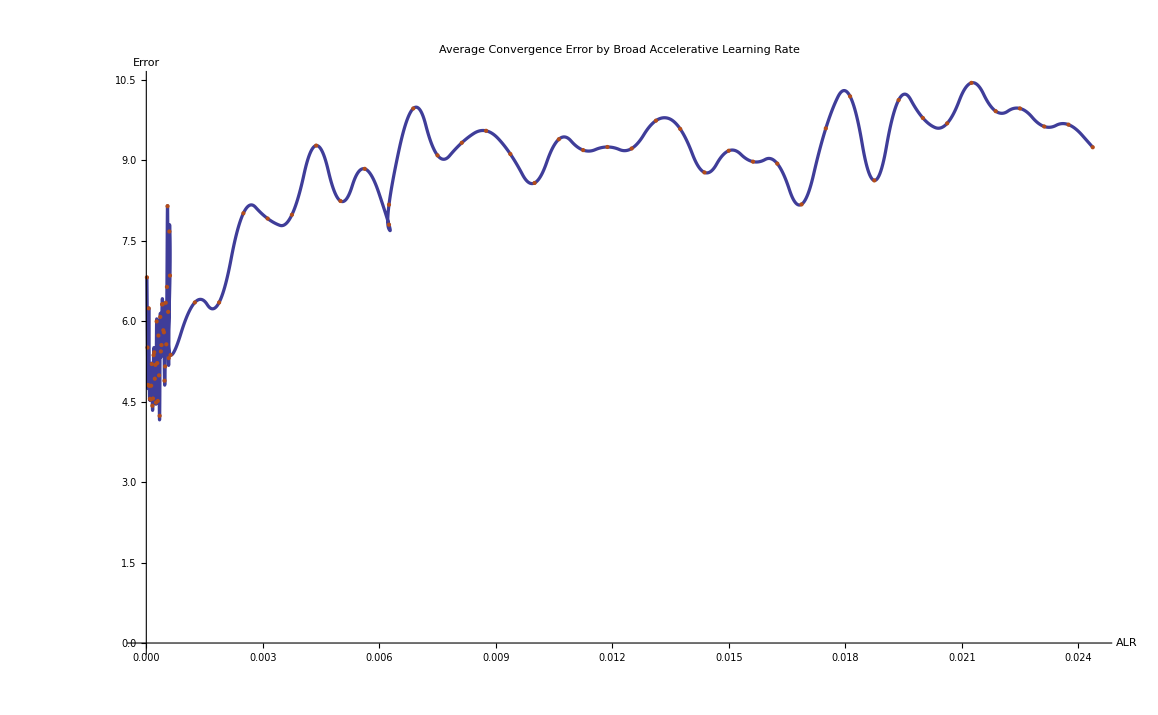

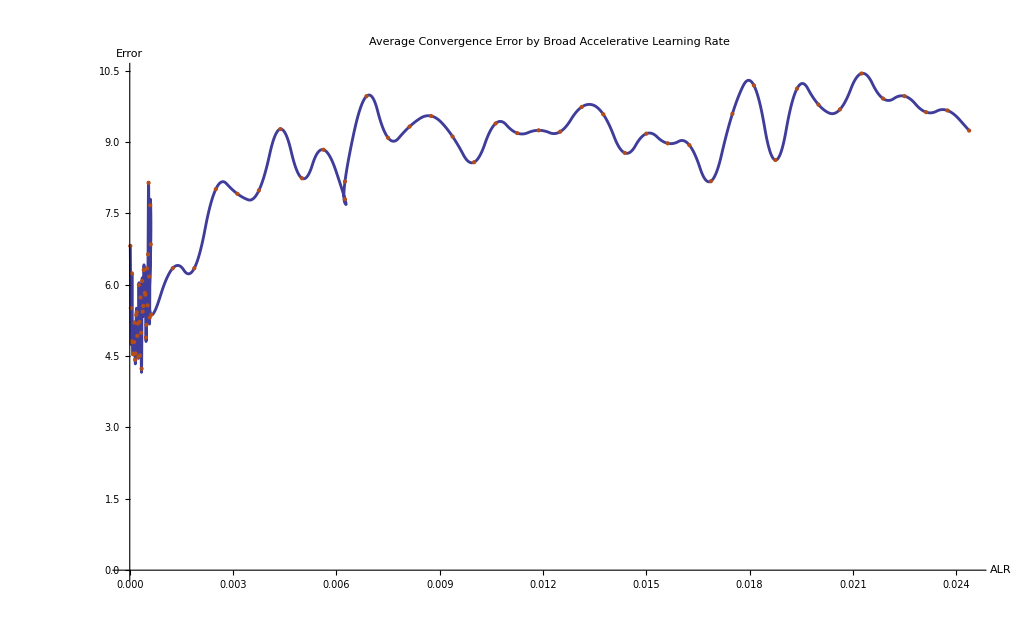

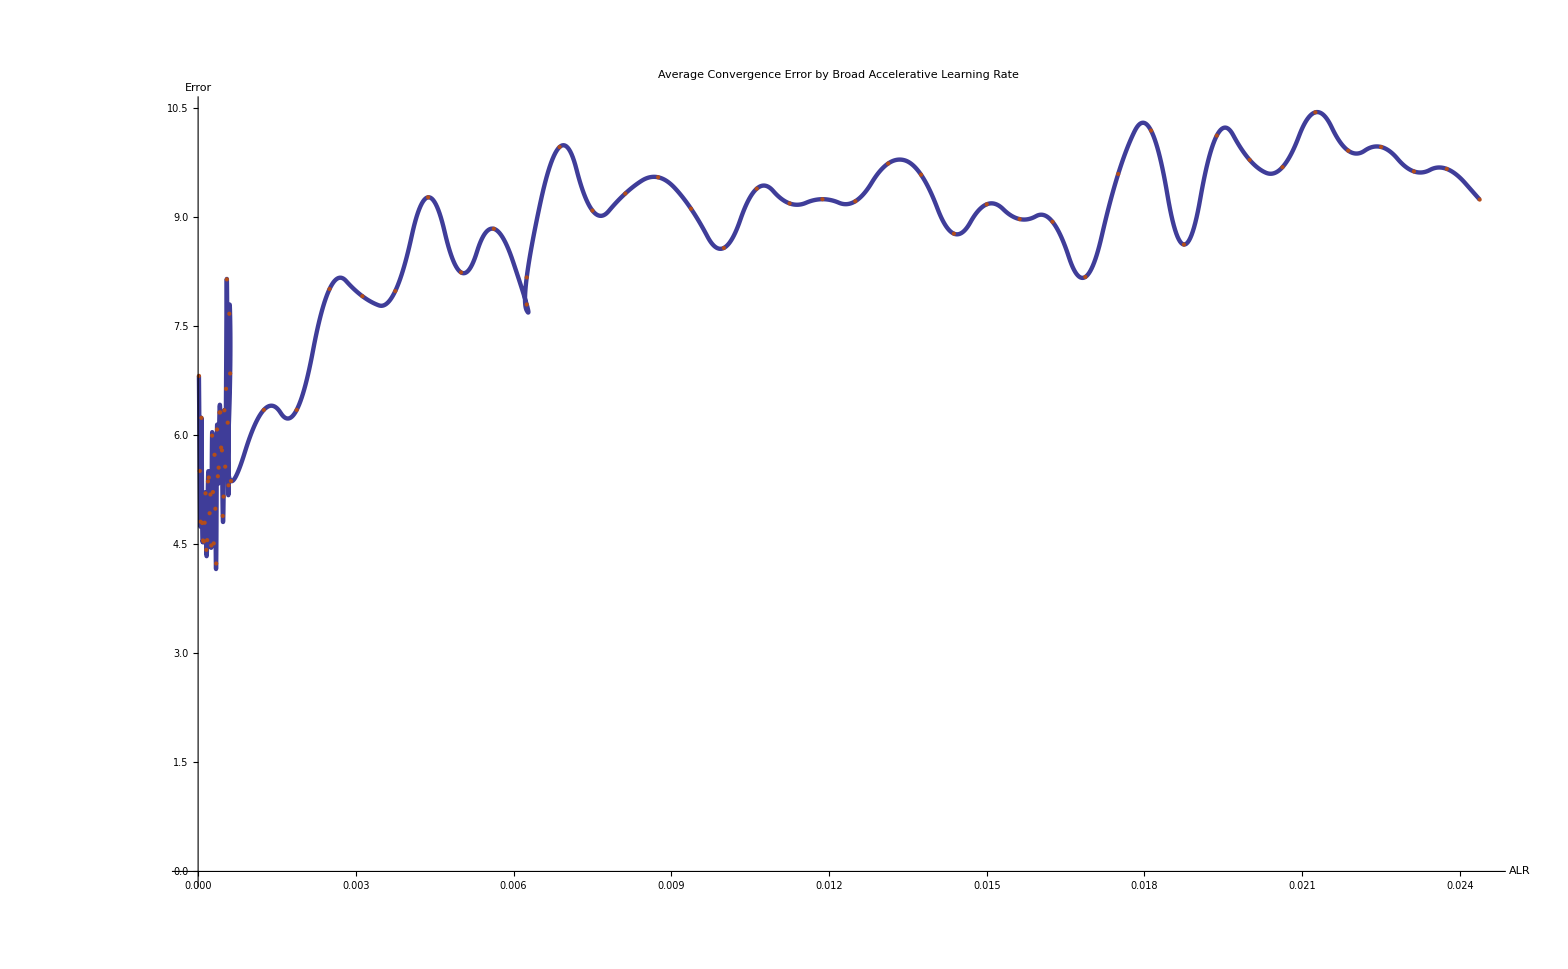

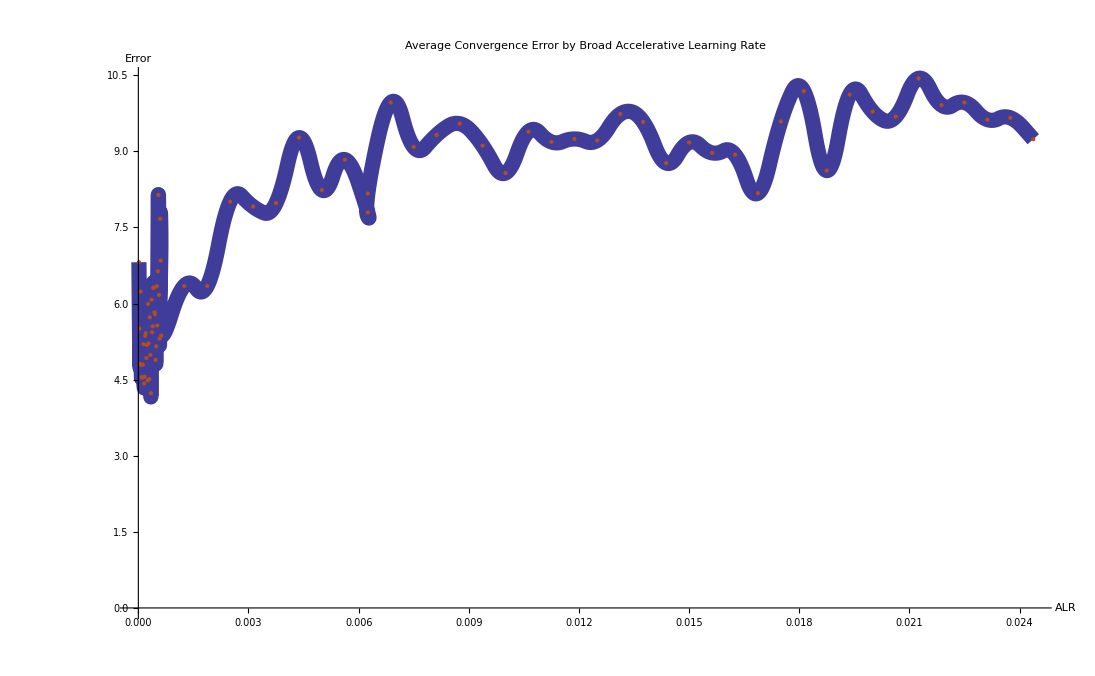

ListPlot::nonopt: Options expected (instead of {{0.000015625, 6.81566}, {0.00003125, 5.50765}, {0.000046875, 4.81025}, {0.0000625, 6.23856}, {0.000078125, 4.79241}, {0.00009375, 4.55171}, {0.000109375, 4.53833}, {0.000125, 4.79578}, {0.000140625, 5.19988}, {0.00015625, 4.42297}, {0.000171875, 4.55651}, {0.0001875, 5.36484}, {0.000203125, 5.41792}, {0.00021875, 4.9263}, {0.000234375, 5.18401}, {0.00025, 4.48303}, {0.000265625, 5.9937}, {0.00028125, 5.21742}, {0.000296875, 4.51148}, {0.0003125, 5.73038}, {0.000328125, 4.98855}, {0.00034375, 4.23498}, {0.000359375, 6.07806}, « 6 », {0.00046875, 4.88941}, {0.000484375, 5.15533}, {0.0005, 6.34175}, {0.000515625, 5.56687}, {0.00053125, 6.63743}, {0.000546875, 8.14239}, {0.0005625, 6.17214}, {0.000578125, 5.31042}, {0.00059375, 7.67005}, {0.000609375, 6.84829}, {0.000625, 5.36893}, {0.00125, 6.34779}, {0.001875, 6.34745}, {0.0025, 8.00981}, {0.003125, 7.91117}, {0.00375, 7.98189}, {0.004375, 9.27159}, {0.005, 8.23829}, {0.005625, 8.8379}, {0.00625, 7.79693}, {0.00625, 8.16954}, « 29 »}) beyond position 3 in ListPlot[BaseStyle → {FontSize → 12}, {{0.000015625, 6.81566}, {0.00003125, 5.50765}, {0.000046875, 4.81025}, {0.0000625, 6.23856}, {0.000078125, 4.79241}, {0.00009375, 4.55171}, {0.000109375, 4.53833}, {0.000125, 4.79578}, {0.000140625, 5.19988}, {0.00015625, 4.42297}, {0.000171875, 4.55651}, {0.0001875, 5.36484}, {0.000203125, 5.41792}, {0.00021875, 4.9263}, {0.000234375, 5.18401}, {0.00025, 4.48303}, {0.000265625, 5.9937}, {0.00028125, 5.21742}, {0.000296875, 4.51148}, {0.0003125, 5.73038}, {0.000328125, 4.98855}, {0.00034375, 4.23498}, « 8 », {0.000484375, 5.15533}, {0.0005, 6.34175}, {0.000515625, 5.56687}, {0.00053125, 6.63743}, {0.000546875, 8.14239}, {0.0005625, 6.17214}, {0.000578125, 5.31042}, {0.00059375, 7.67005}, {0.000609375, 6.84829}, {0.000625, 5.36893}, {0.00125, 6.34779}, {0.001875, 6.34745}, {0.0025, 8.00981}, {0.003125, 7.91117}, {0.00375, 7.98189}, {0.004375, 9.27159}, {0.005, 8.23829}, {0.005625, 8.8379}, {0.00625, 7.79693}, {0.00625, 8.16954}, « 29 »}, PlotStyle → RGBColor[0.7, 0.3, 0.1]]. An option must be a rule or a list of rules.

HlMY1MOfk/bun85+otPOfhd

NXiNlmsYi3Lw+1FTc+SNK6gDfqfndx+z9T2PcvC7h6V6/slRzD/4Xev7q/uo

WuTgt9HTNHHcaFhnu0/9TkyU+2XkqEY5+NXruKp6w04O5bQ+ZyzSarLlUg5+

1y/ul2LahPHg17fi/CPNQjbl4PdHR7nY1jrUAb+OBdts5lawKAe/v44Kvt3M

wXjwWzjp2+/p8cjBb0ff+F7cNOivHlC/Vz4sUXWcyKEc/HYY1zhk7juMB7/F

Eap6L/7e34GD31MslYWrXdmUg9+Ah49O9l+JHPy6Djrd75sei3Lw+6V78OgZ

3pgf8Ht586/kV0moA36fuHz3PBCA+QS/vZ6l/Yq6A/3SQ+q36vy+mFFGfMrB

78rwS6PjfrIpB7+z+97Zn2zHohz8TgycnWZ7HPXBb8vE0wHDfVUpB78WgfYj

T39HHfA7t2tdd/1nyMGvl5fTiRh71Ae/k1JerR7kwaUc/N4dP6JpSwr0P+i3

/7wuI7puZVEOfpu+Gsd9blChHPz6Wd1SV1zGoRz8ykdM3qbwAXXAb2DUroJd

i/iUg98vvdQfnrFTpRz8RuTPNAwz4VIOftsSJj5a5SCgHPzO+/TWa2l/dcrB

r9at6BFFC6DfeET96loMbpt+DTn4rWmIH77IR41y8GslGKtl3VmVcvC7coH2

lKKdPMrBb+v1yKpdPhzKwe8RhRjD7ARMF/ymuRS5zH2K6YLfPosfeKVdRn3w

a/lqcsO0aDbl4DevJfKTkwL0J4+pX+1MLSXjq2zK6f1or1LRDTmMp37fpk28

3olHOfgNDrZ+aJmHOuB33ux9xva6yMHv4keDe/E0UR/8GsXO+X7Ylk85+F1T

+9toqgbGg18rbpz36V0sysFvl/CehYo3oX+opn4PsjYOPhrJpRz8/um3NL0m

DePB77lss09zW3mUg1+XMzu1FQ5wKAe/lk6LXYJeqFEOfoPGpxlalatQDn5X

3/dQf1fMpxz8aqR1PGtEn2dVU79fXlVpDW9hUw5+Fw5Vt1KJh/HVE+q398mN

Sj6j2ZSD32O3FGu52jzKwe/9m99batRQB/x6yn/ptXszi3Lwe7fpxbk9XZGD

X/sFW8OnVGG64Hdmj7n7V3bEdMHvm7Qc+w15mC74DXlvWSavpE45+A1L35GQ

yYPxDPoNOnx+cNddAsrBr+2Nbn3zw7iUg18N9xdj8qNYlINf5zr93UGDOZSD

39BTJ+5et8V0we+JNZNav/ZGDn4Njy2K3hiKOnS8ERqUKH9ZlXI6/62IHP1Z

DfMDfksdeyiS8dBvPKV+j11Y1nZiMJty8JvWzy7KeSZy8Nt4s3p4yR4+5eBX

4fWXtBo1HuXgd7FgbsqBY5gu+J35aeCCprUYD35fDnsStCEV48Hv3iunA6zn

cykHv4mCwM/3HmM87Z9bJuqpf4dxVA31a/w67cPPkyzKwe+cmcIG/dc8ysGv

+8QXWpvVVCgHvxWt16qqVFAf/J5yGFo+MQvjwe+kvFORGn/4lNP5r0m3tqki

zA/4vbV4mnGLOZdy8BtuHD/s62Lk4Df/WK35gWkwLqqlfl8rlVgMquVSDn4n

rylxnx2NHPxePjrHbf1ENcrBb+j8Spdt83mUg9/3yaKs68t7Ug5+P+u9HOJR

y6Ec/L4LmW4ZlcqmHPwO9XruUxWL+Qe/2R5fVYLuqlAOfu817Z2tPRPmcc8Y

v9ZkZa/3i9YRLuUaZk/1FdbbkNBFBkrHD7Mpl14HW9Ld/wO3eg6L8smzxCnb

kSWqD0UtBLn0+tgTv7C4tD1bMV1pvXMgs3ZoHFnwlUO59Lr1JwrXfU4efIf5

eVTydVx90oC//d5y+88OyKXX05EcbrDb/8gRuaCTZ49+FweS3dPu9lywGO6D

6Hfc2+uzj5WpUQ5+J+5f8WHTCIwHv+8szQ5c36RJOfidmT/Kc1ENh3Lwa6Zy

6kUuV0A5+P0++VXhd3d1ysHvrHm7AzPuow74LY0Nfz7rHOYH/HrGvN/4lIXx

4HcnZ8O5UyGwDoZ+fZUd43arIQe/5guVtp19rkY5+F279+PsNRF8ysFvV/O3

Bg6ZXMrBb122ctmbfFXKwe/kDLUFtXEYD34bY/58SVXmUA5+Pf5c+P1ECTn4

dZ4t3JMgFFAOftWHzb2ZqgPt6zn1W/Mw4uiLaRzKwe9Fpea3p10xHvxaZFlm

2N1ToRz8yk1pDDt9kU85+FXfNXKaZxFy8Bu74HUJa7GAcvDbxdl59uMTapSD

X9eGbn8KRmA+we9QpZG+OjdRB/y+Wf3a7/VbuI+g35NLRq+2ckEOfl/YbJsY

m8ylHPx+1tdT1OUjp/U572yYZQcO5eC3x0J/tx4n2JSD3zF5HkqDnQSUg9/9

d1/l99DRoBz8dvD6vtt2uSbl4Hf1yuHuH4PVKQe/GYYzOl2Wh36jjvr9fPL2

dS8vDuXg98Ghox4m47iUg9+duTHLdu/iUw5+u8ez9vXtifHgt9PUXDfThQLK

we+dzv7C2Bwe5eA3ViFTzrsMdcBv4Yf5I166q1MOfnlGs/Y/LcZ48Gt7Rv3E

zUC4n6Lfgfc/14XEcikHv+ErH64yieZTDn537+yzpH4bh3Lwu395v98Xu6E+

+N26+8mxk3LIwW+nE0Uf84YJKAe/wSO/DtzigOmC36GxecGL5JGD3y+/46Le

JqlTDn5Xh/ZltcrDPBH9qhwx7TNlOY9y8GsXMqix6gxy8Lug5LW/xkk+5eD3

6JlXgckvOZSD3+7cvS6T/qhRDn4vXQwdO+AAl3LwuyXnps7nHWzKwe/REYd7

WJVhfsCvyqxu57bpoz74NXbl

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\broad\\broadgraph.dat", "Data"];
Show[ListLinePlot[data, PlotStyle->{Thickness[0.002]},InterpolationOrder->2],
ListPlot[data, PlotStyle-> RGBColor[0.7,0.3,0.1]],AxesLabel->{
Style["ALR", FontSize->20],
Style["Error", FontSize->20]},
         PlotLabel->Style["Average Convergence Error by Broad Accelerative Learning Rate", FontSize->30], BaseStyle ->{FontSize -> 30}]
```

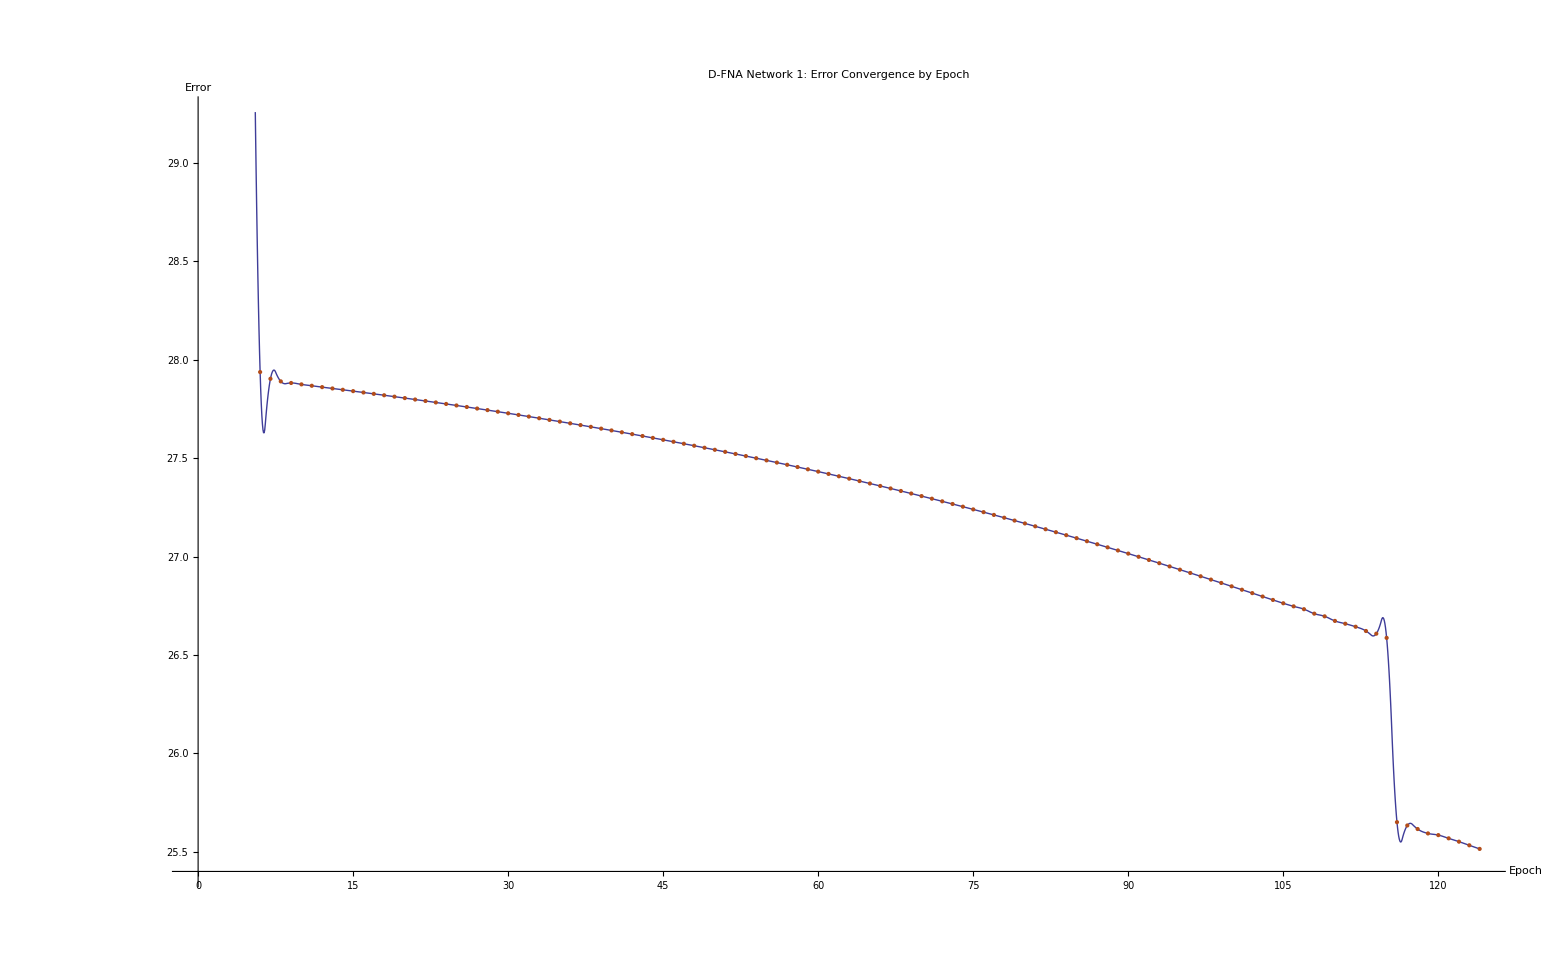

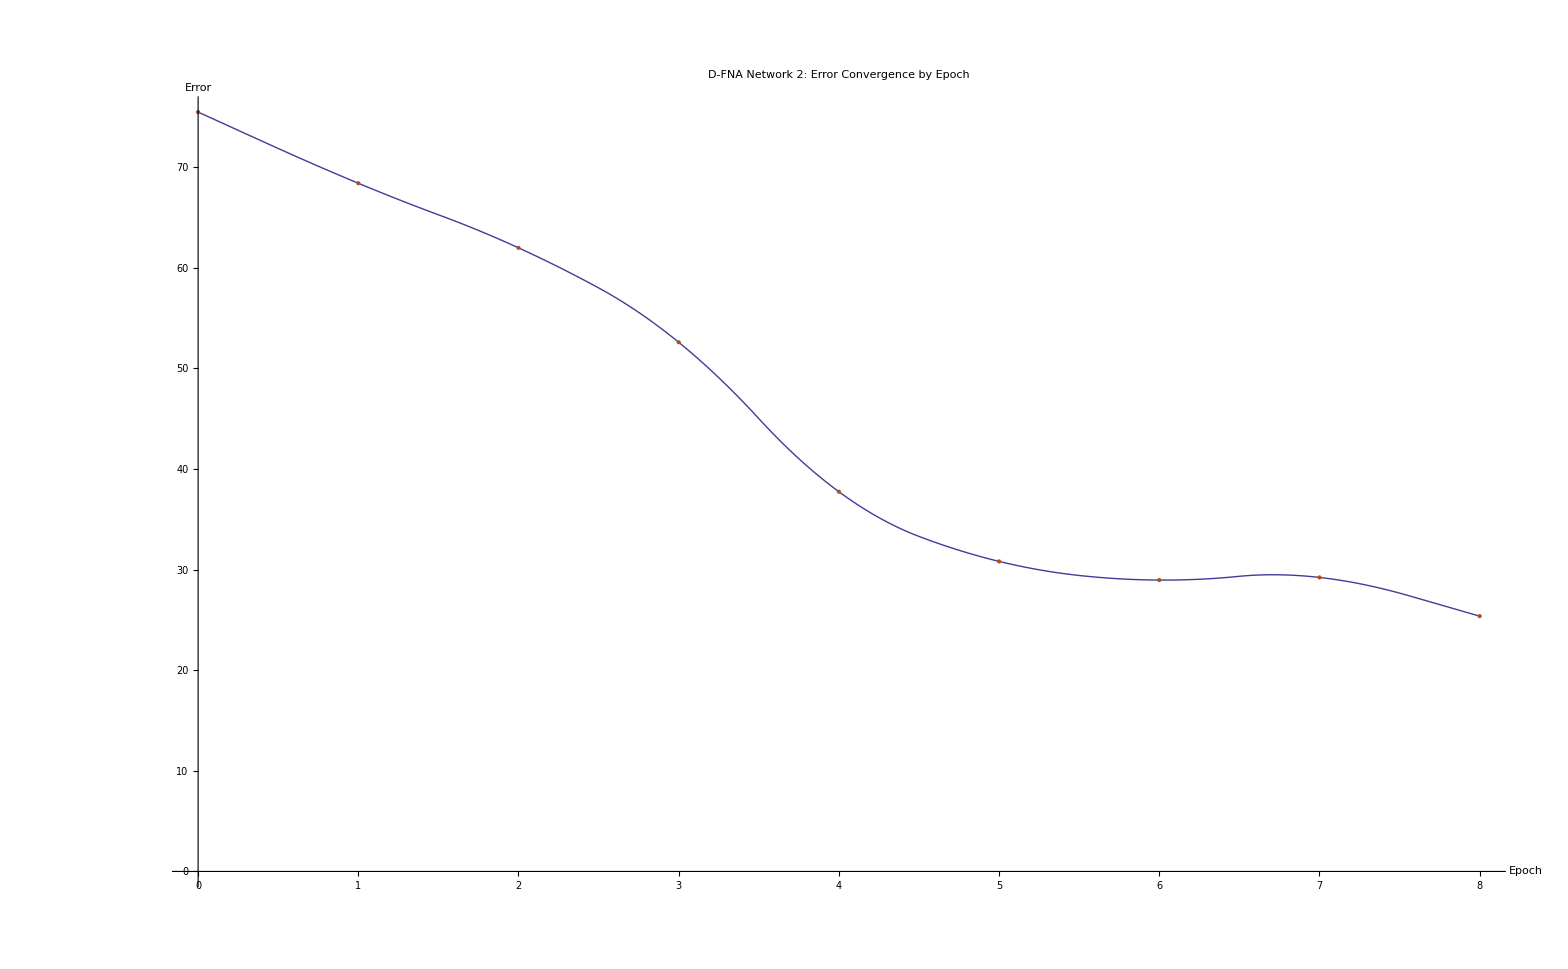

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\0.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->150],Style["Error",FontSize->150]},PlotLabel->Style["D-FNA Network 1: Error Convergence by Epoch",FontSize->160], BaseStyle ->{FontSize -> 120}]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\1.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->150],Style["Error",FontSize->150]},PlotLabel->Style["D-FNA Network 2: Error Convergence by Epoch",FontSize->160], BaseStyle ->{FontSize -> 120}]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\2.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 3: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\3.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 4: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\4.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 5: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\5.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 6: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\6.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 7: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\7.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 8: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\8.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 9: Error Convergence by Epoch",FontSize->36]]
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\conclusion\\9.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],ListPlot[data,PlotStyle->RGBColor[0.7,0.3,0.1]],AxesLabel->{Style["Epoch",FontSize->21],Style["Error",FontSize->21]},PlotLabel->Style["D-FNA Network 10: Error Convergence by Epoch",FontSize->36]]
```

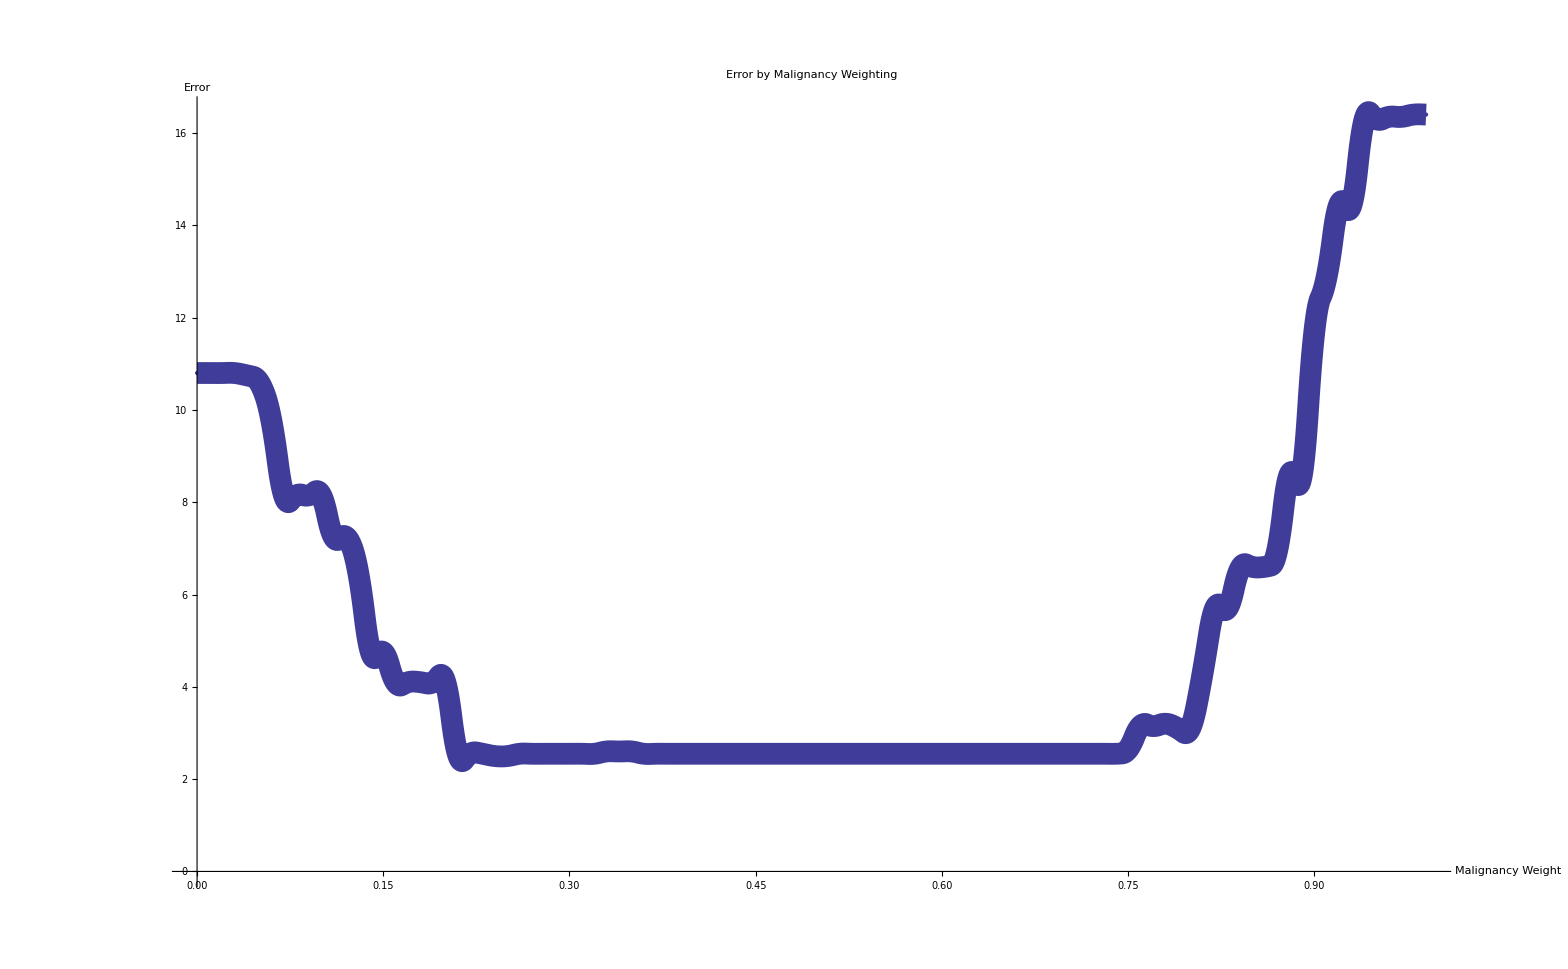

-Graphics-

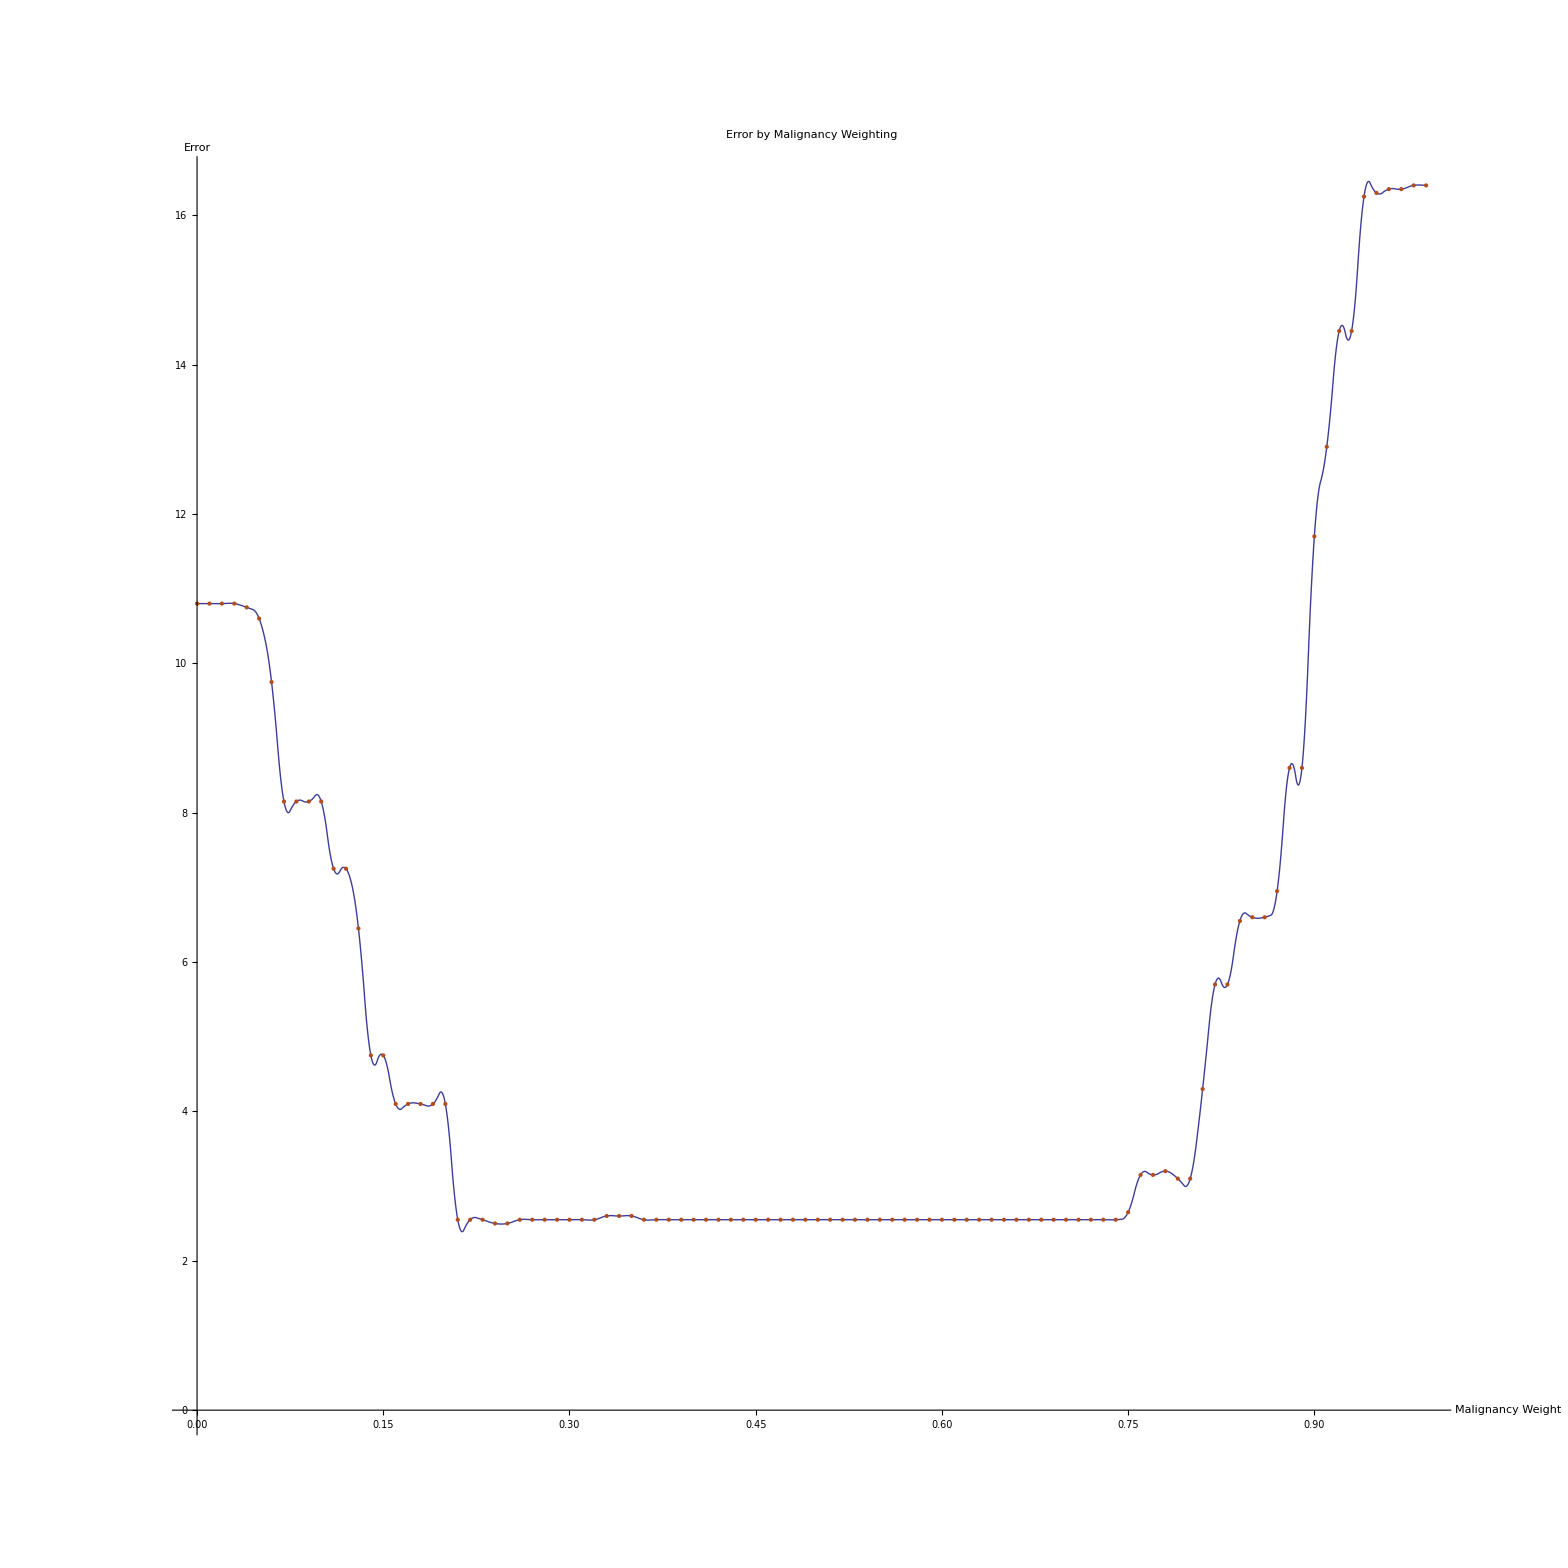

```mathematica
data = Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\WRITEUP\\GRAPHS\\DATA\\step\\step.dat", "Data"];
Show[ListLinePlot[data, PlotStyle-> {Thickness[0.01]},InterpolationOrder->2, AxesLabel->{Style["Malignancy Weight",FontSize->50],Style["Error",FontSize->50]},PlotLabel->Style["Error by Malignancy Weighting",FontSize->100],BaseStyle ->{FontSize -> 40}],ListPlot[data]]
```

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\DATA\\EXPERIMENT\\OUTPUT\\IMAGES\\1\\convergence.dat","Data"];
Show[ListLinePlot[data,InterpolationOrder->2],AxesLabel->{Style["Epoch",FontSize->120],Style["Error",FontSize->120]},PlotLabel->Style["MID Network 1: Error Convergence by Epoch",FontSize->150], BaseStyle ->{FontSize -> 90}]
```

{{0,3.20651},{1,3.14363},{2,3.08645},{3,3.03424},{4,2.98592},{5,2.93208},{6,2.62601},{7,2.58661},{8,2.55086},{9,2.51835},{10,2.48875},{11,2.46176},{12,2.4371},{13,2.41455},{14,2.39387},{15,2.3749},{16,2.35745},{17,2.34136},{18,2.32646},{19,2.31246},{20,2.29835},{21,2.26341},{22,2.57623},{23,2.56582},{24,2.55604},{25,2.54684},{26,2.53818},{27,2.53001},{28,2.5223},{29,2.51502},{30,2.50813},{31,2.50161},{32,2.49543},{33,2.48956},{34,2.48399},{35,2.47869},{36,2.47365},{37,2.46884},{38,2.46426},{39,2.45989},{40,2.45572},{41,2.45173},{42,2.44791},{43,2.44425},{44,2.44074},{45,2.43737},{46,2.43414},{47,2.43103},{48,2.42804},{49,2.42516},{50,2.42239},{51,2.41971},{52,2.41713},{53,2.41464},{54,2.41223},{55,2.4099},{56,2.40764},{57,2.40545},{58,2.40333},{59,2.40128},{60,2.39928},{61,2.39734},{62,2.39546},{63,2.39362},{64,2.39184},{65,2.3901},{66,2.3884},{67,2.38675},{68,2.38513},{69,2.38356},{70,2.38202},{71,2.38051},{72,2.37904},{73,2.3776},{74,2.37619},{75,2.3748},{76,2.37345},{77,2.37212},{78,2.37081},{79,2.36953},{80,2.36827},{81,2.36704},{82,2.36582},{83,2.36462},{84,2.36345},{85,2.36229},{86,2.36115},{87,2.36002},{88,2.35892},{89,2.35783},{90,2.35675},{91,2.35569},{92,2.35464},{93,2.3536},{94,2.35258},{95,2.35157},{96,2.35057},{97,2.34959},{98,2.34861},{99,2.34765},{100,2.34669},{101,2.34575},{102,2.34481},{103,2.34389},{104,2.34297},{105,2.34206},{106,2.34116},{107,2.34027},{108,2.33939},{109,2.33851},{110,2.33765},{111,2.33678},{112,2.33593},{113,2.33508},{114,2.33424},{115,2.33341},{116,2.33258},{117,2.33176},{118,2.33094},{119,2.33013},{120,2.32933},{121,2.32853},{122,2.32773},{123,2.32694},{124,2.32616},{125,2.32538},{126,2.32461},{127,2.32384},{128,2.32307},{129,2.32231},{130,2.32155},{131,2.3208},{132,2.32005},{133,2.31931},{134,2.31857},{135,2.31783},{136,2.3171},{137,2.31637},{138,2.31565},{139,2.31493},{140,2.31421},{141,2.3135},{142,2.31279},{143,2.31208},{144,2.31138},{145,2.31068},{146,2.30998},{147,2.30928},{148,2.30859},{149,2.3079},{150,2.30722},{151,2.30654},{152,2.30586},{153,2.30518},{154,2.30451},{155,2.30384},{156,2.30317},{157,2.30251},{158,2.30184},{159,2.30118},{160,2.30053},{161,2.29987},{162,2.29922},{163,2.29857},{164,2.29793},{165,2.29728},{166,2.29664},{167,2.296},{168,2.29536},{169,2.29473},{170,2.2941},{171,2.29347},{172,2.29284},{173,2.29221},{174,2.29159},{175,2.29097},{176,2.29035},{177,2.28973},{178,2.28912},{179,2.28851},{180,2.2879},{181,2.28729},{182,2.28669},{183,2.28608},{184,2.28548},{185,2.28488},{186,2.28429},{187,2.28369},{188,2.2831},{189,2.28251},{190,2.28192},{191,2.28133},{192,2.28075},{193,2.28016},{194,2.27958},{195,2.279},{196,2.27843},{197,2.27785},{198,2.27728},{199,2.27671},{200,2.27614},{201,2.27557},{202,2.275},{203,2.27444},{204,2.27388},{205,2.27332},{206,2.27276},{207,2.2722},{208,2.27165},{209,2.27109},{210,2.27054},{211,2.26999},{212,2.26944},{213,2.2689},{214,2.26835},{215,2.26781},{216,2.26727},{217,2.26673},{218,2.26619},{219,2.26566},{220,2.26512},{221,2.26459},{222,2.26406},{223,2.26353},{224,2.26301},{225,2.26248},{226,2.26196},{227,2.26143},{228,2.26091},{229,2.2604},{230,2.25988},{231,2.25936},{232,2.25885},{233,2.25834},{234,2.25783},{235,2.25732},{236,2.25681},{237,2.2563},{238,2.2558},{239,2.2553},{240,2.25479},{241,2.25429},{242,2.2538},{243,2.2533},{244,2.2528},{245,2.25231},{246,2.25182},{247,2.25133},{248,2.25084},{249,2.25035},{250,2.24986},{251,2.24938},{252,2.2489},{253,2.24842},{254,2.24794},{255,2.24746},{256,2.24698},{257,2.2465},{258,2.24603},{259,2.24556},{260,2.24509},{261,2.24462},{262,2.24415},{263,2.24368},{264,2.24321},{265,2.24275},{266,2.24229},{267,2.24183},{268,2.24137},{269,2.24091},{270,2.24045},{271,2.23999},{272,2.23954},{273,2.23909},{274,2.23863},{275,2.23818},{276,2.23774},{277,2.23729},{278,2.23684},{279,2.2364},{280,2.23595},{281,2.23551},{282,2.23507},{283,2.23463},{284,2.23419},{285,2.23376},{286,2.23332},{287,2.23289},{288,2.23245},{289,2.23202},{290,2.23159},{291,2.23116},{292,2.23073},{293,2.23031},{294,2.22988},{295,2.22946},{296,2.22903},{297,2.22861},{298,2.22819},{299,2.22777},{300,2.22736},{301,2.22694},{302,2.22652},{303,2.22611},{304,2.2257},{305,2.22529},{306,2.22487},{307,2.22447},{308,2.22406},{309,2.22365},{310,2.22325},{311,2.22284},{312,2.22244},{313,2.22204},{314,2.22164},{315,2.22124},{316,2.22084},{317,2.22044},{318,2.22004},{319,2.21965},{320,2.21926},{321,2.21886},{322,2.21847},{323,2.21808},{324,2.21769},{325,2.2173},{326,2.21692},{327,2.21653},{328,2.21615},{329,2.21576},{330,2.21538},{331,2.215},{332,2.21462},{333,2.21424},{334,2.21386},{335,2.21349},{336,2.21311},{337,2.21273},{338,2.21236},{339,2.21199},{340,2.21162},{341,2.21125},{342,2.21088},{343,2.21051},{344,2.21014},{345,2.20978},{346,2.20941},{347,2.20905},{348,2.20868},{349,2.20832},{350,2.20796},{351,2.2076},{352,2.20724},{353,2.20689},{354,2.20653},{355,2.20617},{356,2.20582},{357,2.20547},{358,2.20511},{359,2.20476},{360,2.20441},{361,2.20406},{362,2.20371},{363,2.20336},{364,2.20302},{365,2.20267},{366,2.20233},{367,2.20198},{368,2.20164},{369,2.2013},{370,2.20096},{371,2.20062},{372,2.20028},{373,2.19994},{374,2.19961},{375,2.19927},{376,2.19893},{377,2.1986},{378,2.19827},{379,2.19794},{380,2.1976},{381,2.19727},{382,2.19694},{383,2.19662},{384,2.19629},{385,2.19596},{386,2.19564},{387,2.19531},{388,2.19499},{389,2.19466},{390,2.19434},{391,2.19402},{392,2.1937},{393,2.19338},{394,2.19306},{395,2.19275},{396,2.19243},{397,2.19211},{398,2.1918},{399,2.19148},{400,2.19117},{401,2.19086},{402,2.19055},{403,2.19024},{404,2.18993},{405,2.18962},{406,2.18931},{407,2.189},{408,2.1887},{409,2.18839},{410,2.18809},{411,2.18778},{412,2.18748},{413,2.18718},{414,2.18688},{415,2.18658},{416,2.18628},{417,2.18598},{418,2.18568},{419,2.18538},{420,2.18509},{421,2.18479},{422,2.1845},{423,2.1842},{424,2.18391},{425,2.18362},{426,2.18333},{427,2.18303},{428,2.18274},{429,2.18246},{430,2.18217},{431,2.18188},{432,2.18159},{433,2.18131},{434,2.18102},{435,2.18074},{436,2.18045},{437,2.18017},{438,2.17989},{439,2.17961},{440,2.17933},{441,2.17905},{442,2.17877},{443,2.17849},{444,2.17821},{445,2.17793},{446,2.17766},{447,2.17738},{448,2.17711},{449,2.17683},{450,2.17656},{451,2.17629},{452,2.17601},{453,2.17574},{454,2.17547},{455,2.1752},{456,2.17493},{457,2.17467},{458,2.1744},{459,2.17413},{460,2.17387},{461,2.1736},{462,2.17334},{463,2.17307},{464,2.17281},{465,2.17255},{466,2.17228},{467,2.17202},{468,2.17176},{469,2.1715},{470,2.17124},{471,2.17098},{472,2.17073},{473,2.17047},{474,2.17021},{475,2.16996},{476,2.1697},{477,2.16945},{478,2.16919},{479,2.16894}}

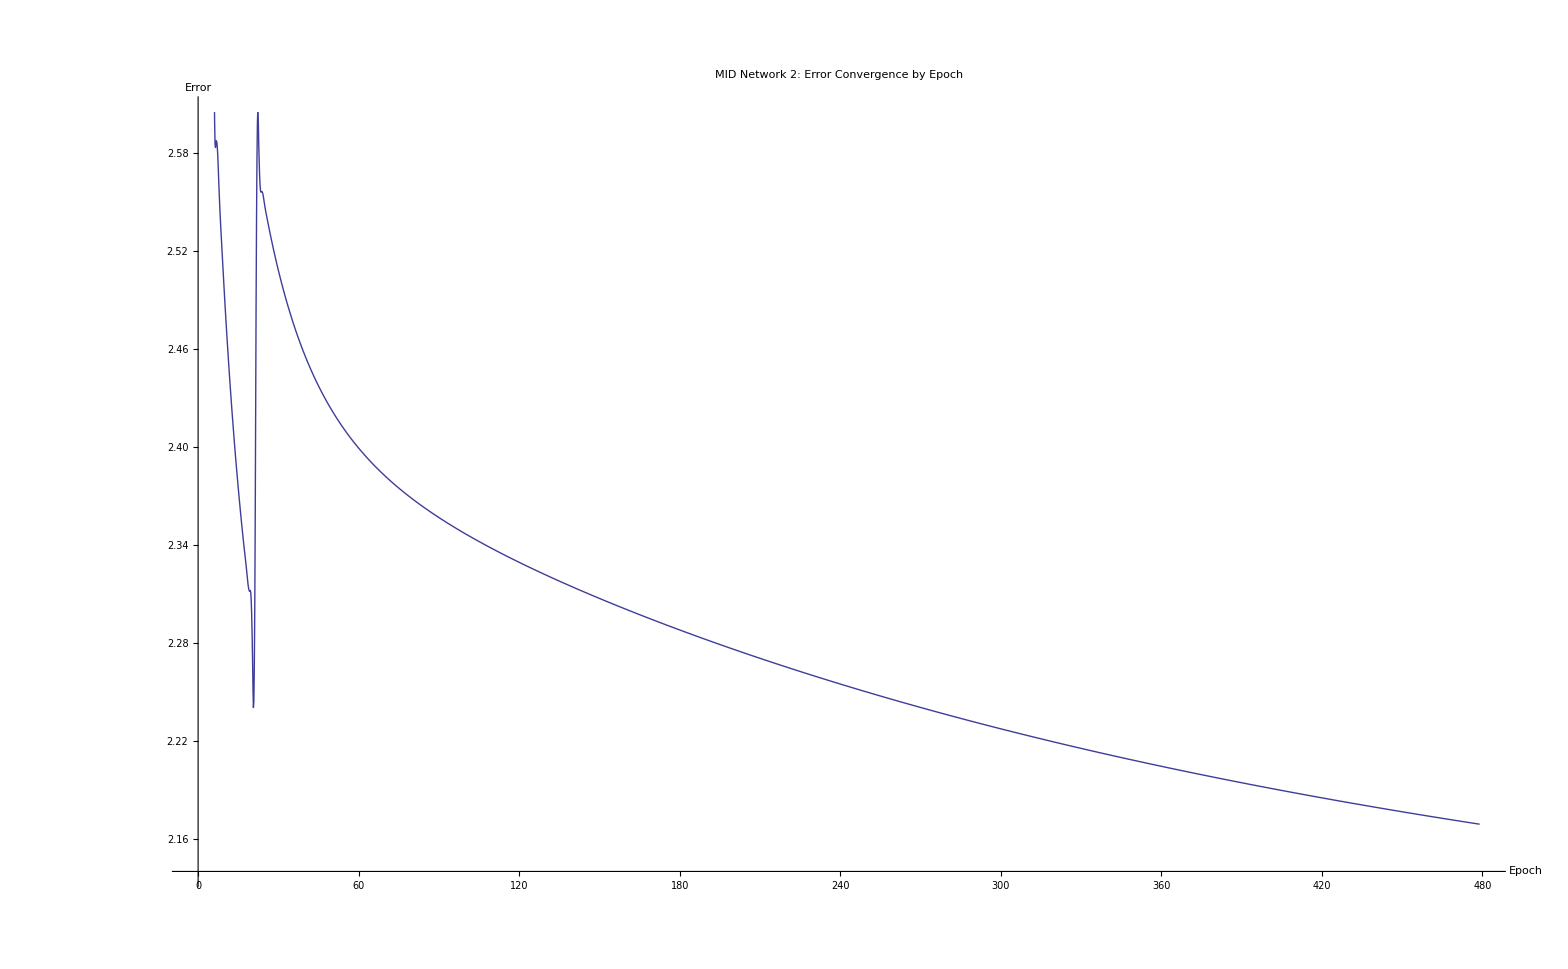

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\DATA\\EXPERIMENT\\OUTPUT\\IMAGES\\2\\convergence.dat","Data"]
Show[ListLinePlot[data,InterpolationOrder->2],AxesLabel->{Style["Epoch",FontSize->120],Style["Error",FontSize->120]},PlotLabel->Style["MID Network 2: Error Convergence by Epoch",FontSize->150], BaseStyle ->{FontSize -> 90}]
```

```mathematica
data=Import["C:\\Users\\William\\Desktop\\ISEFNeuralNetwork\\DATA\\EXPERIMENT\\OUTPUT\\IMAGES\\2\\convergence.dat","Data"9
Show[ListLinePlot[data,InterpolationOrder->2],AxesLabel->{Style["Epoch",FontSize->120],Style["Error",FontSize->120]},PlotLabel->Style["MID Network 2: Error Convergence by Epoch",FontSize->150], BaseStyle ->{FontSize -> 90}]
```